```mathematica
Clear[P0,P1,P2]
```

```mathematica
P0:=1/3(ϵ-4B)
P1:=-α √(ϵ-B)
P2:=+β(1+κ Log[γ √(ϵ-B)])
```

```mathematica
(* ϵ dan P0+P1+P2 : MeV fm^-3 *)
```

```mathematica
Clear[x,α,β,γ,κ]
```

```mathematica
α:=1/(√a4)x
β:=9/12(1-1/a4)x^2
γ:=8/(9 √a4)1/x
κ:=3/(1-1/a4)
```

{0.38278,0.457509,-0.0470959,2.77555,-7.}

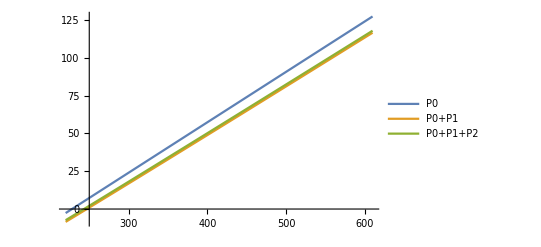

```mathematica
x:=(ms^2/(3π hc^(3/2)))
B:=57.(* MeV fm^-3 *)
a4:=0.7
ms:=100.(* MeV *)
hc:=197.327 (* MeV fm *)
{x,α,β,γ,κ}
Plot[{P0,P0+P1,P0+P1+P2},{ϵ,220,610.},PlotLegends->"Expressions"]
Clear[B,a4,ms,hc,x]
```

```mathematica
Clear[ϵ,ϵ0,ϵ1,ϵ2,ϵ3]
```

```mathematica
ϵ:=ϵ0+ϵ1 x +ϵ2 x^2+ϵ3 x^3
```

```mathematica
eq=-P+P0+P1+P2
```

-P+1/3 (-4 B+ϵ0+x ϵ1+x^2 ϵ2+x^3 ϵ3)-(x √(-B+ϵ0+x ϵ1+x^2 ϵ2+x^3 ϵ3))/(√a4)+3/4 (1-1/a4) x^2 (1+(3 Log[(8 √(-B+ϵ0+x ϵ1+x^2 ϵ2+x^3 ϵ3))/(9 √a4 x)])/(1-1/a4))

```mathematica
Series[eq,{x,0,0}]
```

1/3 (-4 B-3 P+ϵ0)+O[x]^1

```mathematica
Solve[(-4 B-3 P+ϵ0)==0,ϵ0]
```

{{ϵ0→4 B+3 P}}

```mathematica
ϵ0:=4 B+3 P
```

```mathematica
Series[eq,{x,0,1}]
```

(-(√3 √(B+P))/(√a4)+ϵ1/3) x+O[x]^2

```mathematica
Solve[(-(√3 √(B+P))/(√a4)+ϵ1/3)==0,ϵ1]
```

{{ϵ1→(3 √3 √(B+P))/(√a4)}}

```mathematica
ϵ1:=(3 √3 √(B+P))/(√a4)
```

```mathematica
Series[eq,{x,0,2}]
```

((-27+9 a4+4 a4 ϵ2+27 a4 Log[(8 √(B+P))/(3 √3 √a4)]-27 a4 Log[x]) x^2)/(12 a4)+O[x]^3

```mathematica
Solve[(-27+9 a4+4 a4 ϵ2+27 a4 Log[(8 √(B+P))/(3 √3 √a4)]-27 a4 Log[x])==0,ϵ2]//Simplify
```

{{ϵ2→-(9 (-3+a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[x]))/(4 a4)}}

```mathematica
ϵ2:=-(9 (-3+a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[x]))/(4 a4)
```

```mathematica
Series[eq,{x,0,3}]
```

1/(24 a4^(3/2) √(B+P))(-18 √3+36 √3 a4+8 a4^(3/2) √(B+P) ϵ3+27 √3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-27 √3 a4 Log[x]) x^3+O[x]^4

```mathematica
Solve[(-18 √3+36 √3 a4+8 a4^(3/2) √(B+P) ϵ3+27 √3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-27 √3 a4 Log[x])==0,ϵ3]//Simplify
```

{{ϵ3→-(9 √3 (-2+4 a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[x]))/(8 a4^(3/2) √(B+P))}}

```mathematica
ϵ3:=-(9 √3 (-2+4 a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[x]))/(8 a4^(3/2) √(B+P))
```

```mathematica
ϵapprox=ϵ
```

4 B+3 P+(3 √3 √(B+P) x)/(√a4)-(9 x^2 (-3+a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[x]))/(4 a4)-(9 √3 x^3 (-2+4 a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[x]))/(8 a4^(3/2) √(B+P))

```mathematica
ϵsol=ϵapprox/.{x-> ms^2/(3π hc^(3/2))}
```

4 B+3 P+(√3 ms^2 √(B+P))/(√a4 hc^(3/2) π)-(ms^4 (-3+a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[ms^2/(3 hc^(3/2) π)]))/(4 a4 hc^3 π^2)-(ms^6 (-2+4 a4+3 a4 Log[(8 √(B+P))/(3 √3 √a4)]-3 a4 Log[ms^2/(3 hc^(3/2) π)]))/(8 √3 a4^(3/2) hc^(9/2) √(B+P) π^3)

{x,1.19523 x,-0.321429 x^2,1.06243/x,-7.}

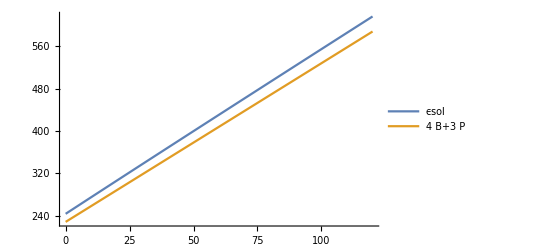

```mathematica
B:=57.(* MeV fm^-3 *)
a4:=0.7
ms:=100.(* MeV *)
hc:=197.327 (* MeV fm *)
{x,α,β,γ,κ}
Plot[{ϵsol,4 B+3 P},{P,0.,120.},PlotLegends->"Expressions"]
Clear[B,a4,ms,hc]
```

```mathematica
ϵlama=3/2(√3 α √(3 α^2+4(Ptl+B))+3 α^2+2(Ptl+B))+B/.{Ptl->P-β(1+κ Log[γ √(3(P+B)+delϵ)])}/.{delϵ->(3 √3)/2 α √(3 α^2+4(P+B))+9/2 α^2}/.{x-> ms^2/(3π hc^(3/2))}//Simplify
```

1/(4 a4 hc^3 π^2)(-(-3+a4) ms^4+4 a4 hc^3 (4 B+3 P) π^2-3 a4 ms^4 Log[1/(3 √a4 ms^2)4 hc^(3/2) √(1/(a4 hc^3)(2 ms^4+12 a4 hc^3 (B+P) π^2+2 √a4 hc^(3/2) ms^2 √((ms^4+12 a4 hc^3 (B+P) π^2)/(a4 hc^3))))]+2 √a4 hc^(3/2) ms^2 √(1/(a4 hc^3)(-(-2+a4) ms^4+12 a4 hc^3 (B+P) π^2-3 a4 ms^4 Log[1/(3 √a4 ms^2)4 hc^(3/2) √(1/(a4 hc^3)(2 ms^4+12 a4 hc^3 (B+P) π^2+2 √a4 hc^(3/2) ms^2 √((ms^4+12 a4 hc^3 (B+P) π^2)/(a4 hc^3))))])))

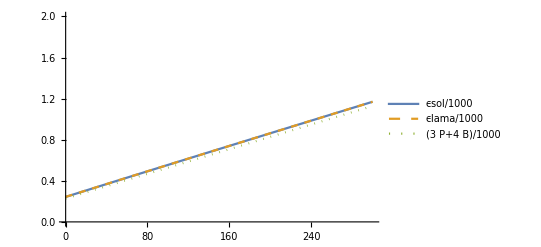

{0.243273,0.24327,0.228}

```mathematica
B:=57.(* MeV fm^-3 *)
a4:=0.7
ms:=100.(* MeV *)
hc:=197.327 (* MeV fm *)
Plot[{ϵsol/1000,ϵlama/1000,(3P+4B)/1000},{P,0.,300.},PlotLegends->"Expressions",PlotStyle->{Default,{Dashed,Thick},Dotted},PlotRange->{0.,2.}]
{ϵsol/1000,ϵlama/1000,(3P+4B)/1000}/.{P->0.}//N
Clear[B,a4,ms,hc]
```

Selesai mengecek energy density
Lanjut mengecek sigma

```mathematica
ϵlama:=3/2(√3 α √(3 α^2+4(Ptl+B))+3 α^2+2(Ptl+B))+B/.{Ptl->P-β(1+κ Log[γ √(3(P+B)+delϵ)])}/.{delϵ->(3 √3)/2 α √(3 α^2+4(P+B))+9/2 α^2}/.{x-> ms^2/(3π hc^(3/2))}//Simplify
```

```mathematica
Clear[α,β,γ,κ,Pc,hc,a4,B,ms,ϵ,ϵc,x]
```

```mathematica
σ:=P-(Pc+(1/3(ϵ-4B)-α √(ϵ-B)+β(1+κ Log[γ √(ϵ-B)]) )-(1/3(ϵc-4B)-α √(ϵc-B)+β(1+κ Log[γ √(ϵc-B)])))
```

```mathematica
α:=1/(√a4)x
β:=9/12(1-1/a4)x^2
γ:=8/(9 √a4)1/x
κ:=3/(1-1/a4)
x:=(ms^2/(3π hc^(3/2)))
```

```mathematica
Pc:=300.
ϵ:=ϵlama
ϵc:=ϵ/.{P->Pc}
```

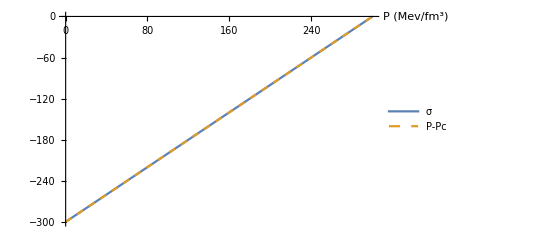

```mathematica
B:=57.(* MeV fm^-3 *)
a4:=0.7
ms:=100.(* MeV *)
hc:=197.327 (* MeV fm *)
Plot[{σ,(P-Pc)},{P,0,Pc},PlotStyle->{Default,Dashed},PlotRange->Automatic,AxesLabel->{"P (Mev/fm^3)",""},PlotLegends->"Expressions"]
```

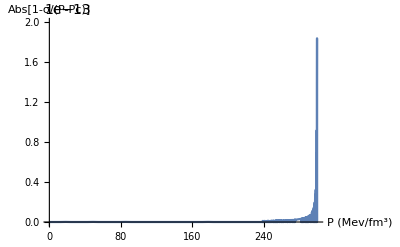

```mathematica
Plot[{Abs[1-σ/(P-Pc)]},{P,0,Pc},PlotStyle->{Default},PlotRange->{0,2*10^-13},AxesLabel->{"P (Mev/fm^3)","Abs[1-σ/(P-Pc)]"}]
```

```mathematica
Clear[ϵ,Pc,ϵc,hc,ms,B,a4]
```